```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v3

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,870,960,10}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,870,960,10}];
r422=chi4/chi2;
r422[[1]]=r422[[1]][[17;;-1]];
r422[[2]][[35;;37]]=0.1;
r422[[2]][[39;;41]]=0.08;
r422[[3]][[29]]=0.17;
r422[[3]][[30]]=0.14;
r422[[3]][[32;;35]]=0.1;
r422[[3]][[39]]=0.05;
```

```mathematica
mub=Table[i,{i,870,960,10}];
T=Table[i,{i,17,120,1}];
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r422[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
Export["r42high.dat",R42all]
```

r42high.dat

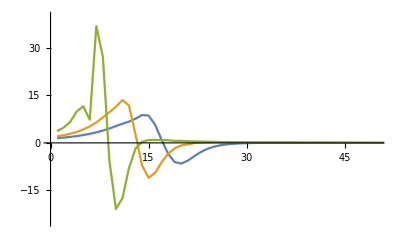

```mathematica
ListLinePlot[r422[[1;;3]],PlotRange->{{0,50},{-25,40}}]
```

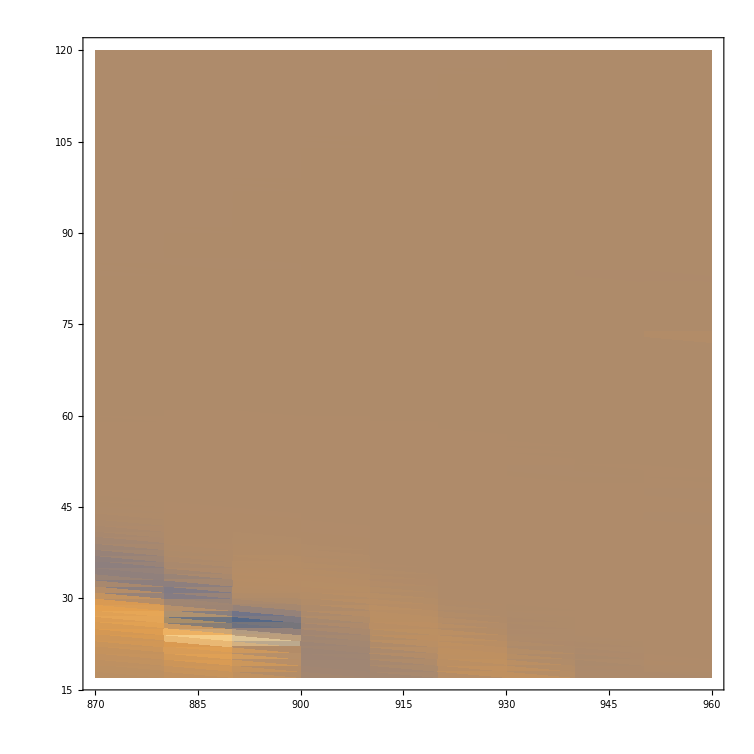

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-25,40}}]
```